```mathematica
ClearAll["Global`*"]
```

```mathematica
(*  *)
```

```mathematica
(* fai il caso più semplice: in Minkowski, assumi il campo dell'inflatone con al soluzione sinusoidale e lo inserisci nell'equazione del campo spettatore, che diventa quella di Mathieu. A questo punto risolta, vedi se i risultati tornano con il "Towards ...pdf" e calcoli il power spectrum di GW.*)
```

# Preheating scenario

```mathematica
Mpl=10^6;                                  (* Planck mass [GeV] *)(* we fix it as 10^6 so m_phi = 10^-6 M_p = 1 *)
mϕ=6*10^-6 Mpl;                    (* inflation mass [GeV] *) (* bounded by CMB *)
g=2.5*10^-4;                                      (* coupling constant ϕ-χ [adim]*)
zMax=20;                            (* ztime [adim] , time [GeV]^-1 *)
Φ0=0.1 Mpl;                                (* initial amplitude ϕ [GeV] *)

qFisico = ((g*Φ0)/(2*mϕ))^2;
A[k_]:=k^2/mϕ^2+2*qFisico;
Print["\n q = ",qFisico]

kLast = qFisico^(1/4);
Print["\n excited k < q^(1/4) = ",kLast]

Print["\n Min A(k=0) = ",A[0]]
Print["\n Max A(k=q^(1/4)) = ",A[kLast]]
```

q = 4.34028

excited k < q^(1/4) = 1.44338

Min A(k=0) = 8.68056

Max A(k=q^(1/4)) = 8.73843

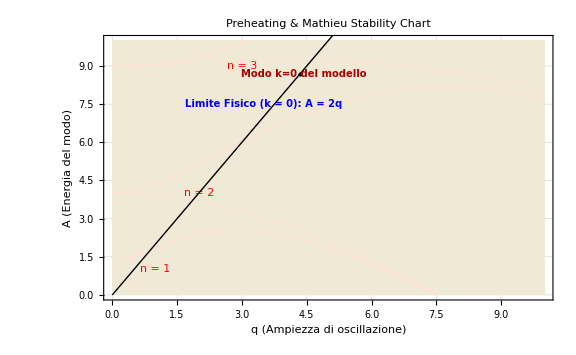

```mathematica
aMin=0;
aMax=10;
qMax=10.;

(*Generazione dello Strutt-Ince stability chart con i dati fisici sovrapposti*)
Plot[{Table[MathieuCharacteristicA[n,qvar],{n,0,5}],Table[MathieuCharacteristicB[n,qvar],{n,1,5}]},{qvar,0,qMax},PlotRange->{aMin,aMax},GridLines->Automatic,Frame->True,FrameLabel->{"q (Ampiezza di oscillazione)","A (Energia del modo)"},PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed,Thick]},ColorFunction->Function[{qvar,A},If[(A>MathieuCharacteristicA[0,qvar]&&A<MathieuCharacteristicB[1,qvar])||(A>MathieuCharacteristicA[1,qvar]&&A<MathieuCharacteristicB[2,qvar])||(A>MathieuCharacteristicA[2,qvar]&&A<MathieuCharacteristicB[3,qvar])||(A>MathieuCharacteristicA[3,qvar]&&A<MathieuCharacteristicB[4,qvar]),RGBColor[0.88,0.95,0.86],RGBColor[1.0,0.88,0.82]]],ColorFunctionScaling->False,Filling->Axis,PlotLabel->Style["Preheating & Mathieu Stability Chart",Bold,14],ImageSize->Large,Epilog->{Text[Style["n = 1",Red,11],{1.0,1.0}],Text[Style["n = 2",Red,11],{2.0,4.0}],Text[Style["n = 3",Red,11],{3.0,9.0}],Style[Line[{{0,0},{qMax,2*qMax}}],Blue,Thick],Text[Style["Limite Fisico (k = 0): A = 2q",Blue,Bold,10],{3.5,7.5},{-1,0}],Style[Point[{qFisico,2*qFisico}],Red,PointSize[0.015]],Text[Style["Modo k=0 del modello",Darker[Red],Bold,10],{qFisico+0.1,2*qFisico},{-1,0}]}]
```

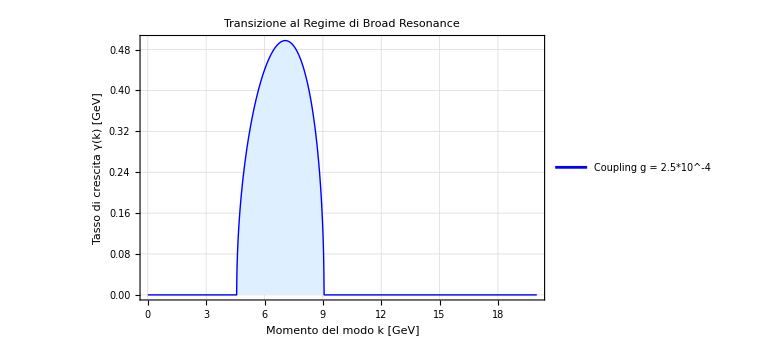

```mathematica
(*2. Definizione della funzione per il calcolo del tasso di crescita fisico*)
tassoCrescita[k_,qVal_]:=Module[{AVal,nu},AVal=k^2/mϕ^2+2*qVal;
nu=MathieuCharacteristicExponent[AVal,qVal];
If[Element[nu,Reals],0.0,Abs[Im[nu]]*(mϕ/2)]]

(*3. Grafico di confronto degli spettri di produzione*)
Plot[tassoCrescita[k,qFisico],{k,0,20},PlotRange->All,Frame->True,FrameLabel->{"Momento del modo k [GeV]","Tasso di crescita γ(k) [GeV]"},PlotStyle->{Directive[Blue,Thick]},Filling->{1->{Axis,LightBlue}},PlotLegends->Placed[LineLegend[{Style["Coupling g = 2.5*10^-4",11]},LegendFunction->"Panel"],Above],PlotLabel->Style["Transizione al Regime di Broad Resonance",Bold,14],GridLines->Automatic,ImageSize->Large]
```

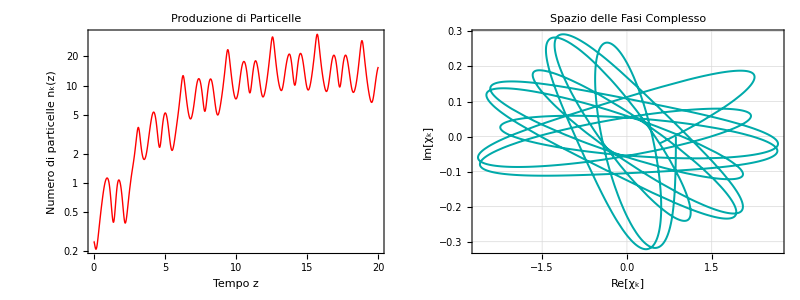

```mathematica
(* Frequency *)
ω2[z_,k_]:=A[k]-2 qFisico* Cos[2 z];
ω[z_,k_]:=√ω2[z,k];

(* EOM daughter χ *)
eqχ=χ''[z]+ω2[z,k]*χ[z]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0,k])),χ'[0]==-I*√(ω[0,k]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=ParametricNDSolveValue[{eqχ,χconditions[[1]],χconditions[[2]]},χ,{z,0,zMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];

(* Daughter solution *)
χsol[k_,t_]:=solχ[k][t];

(* Number density particles *)
numberχ[t_,k_] := Module[{χsolK},
χsolK = solχ[k];
Abs[χsolK'[t]]^2/ω[t,k]+ω[t,k]/2 Abs[χsolK[t]]^2-1/2
];

kScelto = 4.;
Grid[{{LogPlot[numberχ[z,kScelto],{z,0,zMax},PlotRange->All,Frame->True,FrameLabel->{"Tempo z","Numero di particelle n_k(z)"},PlotStyle->{Red,Thick},PlotLabel->Style["Produzione di Particelle",Bold,12],ImageSize->Medium,GridLines->Automatic],ParametricPlot[{Re[χsol[kScelto,z]],Im[χsol[kScelto,z]]},{z,0,zMax},PlotRange->All,Frame->True,FrameLabel->{"Re[χ_k]","Im[χ_k]"},PlotStyle->Directive[Darker[Cyan],Thickness[0.004]],PlotLabel->Style["Spazio delle Fasi Complesso",Bold,12],ImageSize->Medium,GridLines->Automatic]}}]
```

```mathematica
χsol'[k,z]
```

χsol'[k,z]

D::ivar: 0.000408571 is not a valid variable.

D::ivar: 0.408572 is not a valid variable.

D::ivar: 0.816735 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

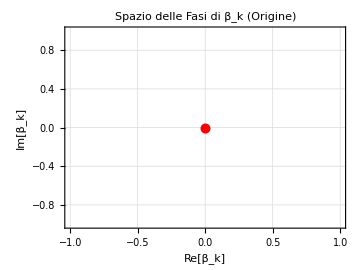
-Graphics- | -Graphics-

```mathematica
solKχ=solχ[k];
αk[z_,k_]:=1/(√(2*ω[z,k]))(ω[z,k]*χsol[k,z]+I*χsol'[k,z]);
βk[z_,k_]:=1/(√(2*ω[z,k]))(ω[z,k]*χsol[k,z]-I*D[χsol[k,z],z]);


Grid[{{Plot[Abs[βk[z,kScelto]]^2,{z,0,zMax},PlotRange->All,Frame->True,FrameLabel->{"Tempo z","Numero di particelle N_k(z)"},PlotStyle->{Red,Thick},PlotLabel->Style["N_k(z) = |β_k|^2 (Inizio da 0)",Bold,11],GridLines->Automatic,ImageSize->Medium],
ParametricPlot[{Re[βk[z,kScelto]],Im[βk[z,kScelto]]},{z,0,zMax},PlotRange->All,Frame->True,FrameLabel->{"Re[β_k]","Im[β_k]"},PlotStyle->Directive[Orange,Thickness[0.004]],PlotLabel->Style["Spazio delle Fasi di β_k (Origine)",Bold,11],GridLines->Automatic,ImageSize->Medium,Epilog->{Red,PointSize[0.02],Point[{0,0}]}]}}]
```

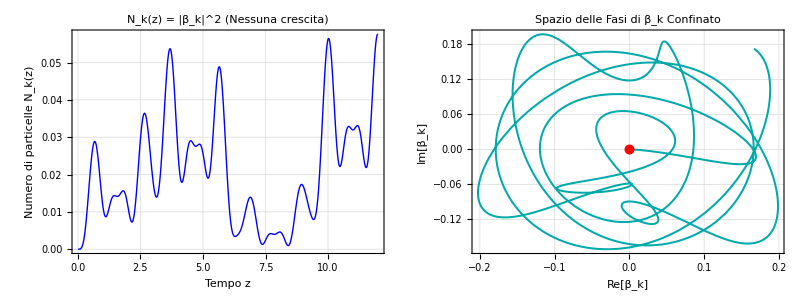

```mathematica
(*1. Parametri fisici*)Mpl=10^6;
mϕ=6*10^-6 Mpl;
Φ0=0.1 Mpl;
gForte=2.5*10^-4;

qFisico=((gForte*Φ0)/(2*mϕ))^2;

(*Scegliamo un modo k ad alta energia FUORI dalle lingue di risonanza*)
kStabile=12.0;
aVal=kStabile^2/mϕ^2+2*qFisico;

(*Frequenza iniziale esatta al tempo z=0*)
ωini=Sqrt[aVal-2*qFisico];

(*Condizioni Iniziali del Vuoto di Bunch-Davies*)
chi0=1/Sqrt[2*ωini];
dchi0=-I*Sqrt[ωini/2];

zMax=12;

(*2. Risoluzione numerica complessa*)
solComplex=NDSolveValue[{chi''[z]+(aVal-2 qFisico Cos[2 z]) chi[z]==0,chi[0]==chi0,chi'[0]==dchi0},chi,{z,0,zMax}];

(*Frequenza istantanea adiabatica*)
ω[z_]:=Sqrt[Max[0.001,aVal-2 qFisico Cos[2 z]]];

(*3. Coefficienti di Bogoliubov*)
αk[z_]:=(ω[z]*solComplex[z]+I*solComplex'[z])/(Sqrt[2*ω[z]]);
βk[z_]:=(ω[z]*solComplex[z]-I*solComplex'[z])/(Sqrt[2*ω[z]]);

(*4. Grafici per la regione STABILE*)
Grid[{{(*Grafico 1:Numero di particelle oscillante ma confinato*)Plot[Abs[βk[z]]^2,{z,0,zMax},PlotRange->{0,All},Frame->True,FrameLabel->{"Tempo z","Numero di particelle N_k(z)"},PlotStyle->{Blue,Thick},PlotLabel->Style["N_k(z) = |β_k|^2 (Nessuna crescita)",Bold,11],GridLines->Automatic,ImageSize->Medium],(*Grafico 2:Lo spazio delle fasi racchiuso in un'orbita chiusa*)ParametricPlot[{Re[βk[z]],Im[βk[z]]},{z,0,zMax},PlotRange->All,Frame->True,FrameLabel->{"Re[β_k]","Im[β_k]"},PlotStyle->Directive[Darker[Cyan],Thickness[0.004]],PlotLabel->Style["Spazio delle Fasi di β_k Confinato",Bold,11],GridLines->Automatic,ImageSize->Medium,(*Origine evidenziata*)Epilog->{Red,PointSize[0.02],Point[{0,0}]}]}}]
```

## Solve:

```mathematica
ω2[z_,k_]:=A[k]-2*q*Cos[2*z];
ω[z_,k_]:=√ω2[z,k];

(* EOM daughter χ *)
eqnχ=χ''[z]+ω2[z,k]*χ[z]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0,k])),χ'[0]==-I*√(ω[0,k]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=ParametricNDSolveValue[{eqnχ,χconditions[[1]],χconditions[[2]]},χ,{z,0,zMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];

(* Solution χ *)
χsol[k_,z_]:=solχ[k][z];

(* Number density particles *)
numberχ[z_,k_] := Module[{χsolK},
χsolK = solχ[k];
Abs[χsolK'[z]]^2/ω[z,k]+ω[z,k]/2 Abs[χsolK[z]]^2-1/2
];
```

```mathematica
kprova =.5;

(*3. Generazione dei grafici*)
Grid[{{(*Grafico 1:Soluzione χ(z) in funzione del tempo z*)Plot[Evaluate[Abs[χsol[kprova,z]]],{z,0,zMax},PlotRange->All,Frame->True,FrameLabel->{"z","χ(z)"},PlotStyle->Blue,PlotLabel->Style[StringForm["Traiettoria (A = ``, q = ``)",A[kprova],q],Bold,12],ImageSize->Medium,GridLines->Automatic],ParametricPlot[Evaluate[{Re[χsol[kprova,z]],Re[D[χsol[kprova,z],z]]}],{z,0,zMax},PlotRange->All,Frame->True,FrameLabel->{"χ","dχ/dz"},PlotStyle->Darker[Purple],PlotLabel->Style["Spazio delle Fasi",Bold,12],ImageSize->Medium,GridLines->Automatic]}}]
```

-Graphics- | -Graphics-

## Power spectrum of the Daughter field

```mathematica
PSχ[k_,z_]:=k^3/(2 π^2)  Abs[χsol[k,z]]^2 ;

χSpectrum[kList_List,z_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,PSχ[k,z]},{k,kList}],Row[{"Computation χ for k = ",currentK}]]
];

nχSpectrum[kList_List,z_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,numberχ[z,k]},{k,kList}],Row[{"Computation nχ for k = ",currentK}]]
];
```

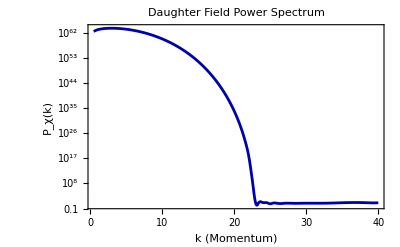

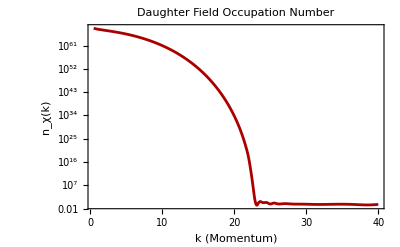

```mathematica
(* Range values *)
kValsχ=Range[0.5,40.0,0.5];

spectrumχ=χSpectrum[kValsχ,zMax];
spectrumnχ=nχSpectrum[kValsχ,zMax];

(* Plot *)
plotSpectrumχ=ListLogPlot[spectrumχ,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"k (Momentum)","P_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Blue]},GridLines->Automatic,PlotLabel->"Daughter Field Power Spectrum"]

plotSpectrumnχ=ListLogPlot[spectrumnχ,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"k (Momentum)","n_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Red]},GridLines->Automatic,PlotLabel->"Daughter Field Occupation Number"]
```

# GW

## Compute the Power spectrum of GWs

```mathematica
(*  ,  *)
TimeIntegral[k_,p_,x_,τ_]:=Module[{kp,Ic,Is},
kp=Sqrt[k^2+p^2-2*k*p*x];

Quiet[
Ic=NIntegrate[Cos[k*t]*χsol[p,t]*χsol[kp,t],{t,0,τ},Method->"LocalAdaptive",MaxRecursion->15,AccuracyGoal->5,PrecisionGoal->5];
Is=NIntegrate[Sin[k*t]*χsol[p,t]*χsol[kp,t],{t,0,τ},Method->"LocalAdaptive",MaxRecursion->15,AccuracyGoal->5,PrecisionGoal->5];
];

(*  *)
(1-x^2)^2*(Abs[Ic]^2+Abs[Is]^2)*p^6
];

(*  *)
GWGrid[k_,τ_,pMax_:10.0,dp_:0.5,dx_:0.1]:=Module[{grid},
grid=Flatten[ParallelTable[{{p,x},TimeIntegral[k,p,x,τ]},{p,0.01,pMax,dp},{x,-1.0,1.0,dx}],1];
grid
];

funzρGWO[k_,τ_,pMax_:10.0,dp_:0.5,dx_:0.1]:=Module[{gridData,interpFunc,res},
gridData=GWGrid[k,τ,pMax,dp,dx];
interpFunc=Interpolation[gridData,InterpolationOrder->2];

(* integrate *)
res=NIntegrate[interpFunc[p,x],{p,0.01,pMax},{x,-1,1},Method->"GlobalAdaptive",AccuracyGoal->4,PrecisionGoal->4];
k^3/(2 π^3) *res
];

GWSpectrum[kList_List,τ_,pMax_:10.0,dp_:0.5,dx_:0.1]:=Module[{currentK},

Monitor[Table[currentK=k;{k,funzρGWO[k,τ,pMax,dp,dx]},{k,kList}],Row[{"Calculating spectrum... currently evaluating k = ",currentK}]]
];
```

## Power spectrum

```mathematica
DiscreteTimeIntegral[k_,p_,x_,τ_,tSteps_:150]:=Module[{tList,dt,χ1,χ2,kp,cosVec,sinVec,IntegrandCos,IntegrandSin,Ic,Is},
kp=Sqrt[k^2+p^2-2*k*p*x];
dt=τ/tSteps;
tList=Range[0.,τ,dt];

χ1=Table[χsol[p,t],{t,tList}];
χ2=Table[χsol[kp,t],{t,tList}];

cosVec=Cos[k*tList];
sinVec=Sin[k*tList];

IntegrandCos=cosVec*χ1*χ2;
IntegrandSin=sinVec*χ1*χ2;

Ic=(dt/2)*(IntegrandCos[[1]]+2*Sum[IntegrandCos[[i]],{i,2,tSteps}]+IntegrandCos[[-1]]);
Is=(dt/2)*(IntegrandSin[[1]]+2*Sum[IntegrandSin[[i]],{i,2,tSteps}]+IntegrandSin[[-1]]);

(1-x^2)^2*(Abs[Ic]^2+Abs[Is]^2)*p^6
];


FastGWSpectrumPoint[k_,τ_,pMax_:10.0,dp_:0.5,dx_:0.1,tSteps_:150]:=Module[{pList,xList,totalSum,pVal,xVal,term},
pList=Range[0.05,pMax,dp];
xList=Range[-0.95,0.95,dx];

totalSum=ParallelSum[term=DiscreteTimeIntegral[k,pVal,xVal,τ,tSteps];
term*dp*dx,{pVal,pList},{xVal,xList}];
(k^3/(2*Pi^3))*totalSum];

(*3. Spectrum Wrapper*)
FastGWSpectrum[kList_List,τ_,pMax_:10.0,dp_:0.5,dx_:0.1,tSteps_:150]:=Module[{currentK,result},
Monitor[result=Table[currentK=k;
{k,FastGWSpectrumPoint[k,τ,pMax,dp,dx,tSteps]},{k,kList}];
result,Row[{"Evaluating GW point for k = ",currentK}]]];
```

```mathematica
kValsGW=Range[0.2,8,0.2];
spectrumGW=FastGWSpectrum[kValsGW,tMax];
```

```mathematica
DiscreteTimeIntegral[k_,p_,x_,τ_,dt_:0.01]:=Module[{tList,χ1,χ2,kp,cosVec,sinVec,IntegrandCos,IntegrandSin,Ic,Is},
kp=Sqrt[k^2+p^2-2*k*p*x];
tList=Range[0.,τ,dt];

Quiet[
χ1=solχ[p][tList];
χ2=solχ[kp][tList];
];
cosVec=Cos[k*tList];
sinVec=Sin[k*tList];

IntegrandCos=cosVec*χ1*χ2;
IntegrandSin=sinVec*χ1*χ2;

Ic=(dt/2)*(Total[IntegrandCos]*2-IntegrandCos[[1]]-IntegrandCos[[-1]]);
Is=(dt/2)*(Total[IntegrandSin]*2-IntegrandSin[[1]]-IntegrandSin[[-1]]);

(1-x^2)^2*(Abs[Ic]^2+Abs[Is]^2)*p^6
];


FastGWSpectrumPoint[k_,τ_,pMax_:10.0,dp_:0.1,dx_:0.05]:=Module[{pList,xList,totalSum,pVal,xVal,term},
pList=Range[0.05,pMax,dp];
xList=Range[-0.95,0.95,dx];

totalSum=ParallelSum[term=DiscreteTimeIntegral[k,pVal,xVal,τ];
term*dp*dx,{pVal,pList},{xVal,xList}];
(k^3/(2*Pi^3))*totalSum
];


FastGWSpectrum[kList_List,τ_,pMax_:10.0,dp_:0.1,dx_:0.05]:=Module[{currentK,result},
Monitor[result=Table[currentK=k;
{k,FastGWSpectrumPoint[k,τ,pMax,dp,dx]},{k,kList}];
result,Row[{"Evaluating CORRECTED GW point for k = ",currentK}]]];
```

```mathematica
kValsGW=Range[0.1,8,0.5];
spectrumGW=FastGWSpectrum[kValsGW,tMax];
plotData=Transpose[{kValsGW,spectrumGW[[All,2]]}];

scientificPlot=ListLogPlot[plotData,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontFamily->"Times",FontSize->14},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->500]
```

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},Symbol[]} cannot be transposed.

ListLogPlot::lpn: { is not a list of numbers or pairs of numbers.

ListLogPlot[Transpose[{{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},Symbol[]}],Joined→True,InterpolationOrder→2,PlotRange→All,Frame→True,Axes→False,PlotStyle→Directive[GrayLevel[0],Thickness[0.004]],BaseStyle→{FontFamily→Times,FontSize→14},GridLines→Automatic,GridLinesStyle→Directive[GrayLevel[0.8],Dashing[{Small,Small}]],ImageSize→500]

## Save data

```mathematica
(* Power spectrum χ *)
fileNameχCSV="DaughterSpectrumPreheating.csv";
fileNamenχCSV="DaughterNumberParticleSpectrumPreheating.csv";
fileNameGWCSV="GWSpectrumPreheating.csv";

Print["Saving data to: ",NotebookDirectory[],"\\",fileNameχCSV];
Export[fileNameχCSV,spectrumχ];
Print["Saving data to: ",NotebookDirectory[],"\\",fileNamenχCSV];
Export[fileNamenχCSV,spectrumnχ];
Print["Saving data to: ",NotebookDirectory[],"\\",fileNameGWCSV];
Export[fileNameGWCSV,spectrumGW];
```

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\DaughterSpectrumPreheating.csv

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\DaughterNumberParticleSpectrumPreheating.csv

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\GWSpectrumPreheating.csv

```mathematica
(* Import the saved data
savedSpectrumχ = Import["DaughterSpectrumPreheating.csv"];
savedSpectrumnχ = Import["DaughterNumberParticleSpectrumPreheating.csv"];
savedSpectrumGW = Import["GWSpectrumPreheating.csv"]*)
```